```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b"]
vo2Data=ReadList["exp10_30_counter_q_omega1old_omega2old_omega0R_tempFrac_qFrac_omega1new_omega2new.out",{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
Tc=340.65;
T0=329.65;
omega0R=-10.7507508144;
```

```mathematica
originalBandA=Transpose@{Transpose[vo2Data][[1]],Transpose[vo2Data][[3]]};
originalBandB=Transpose@{Transpose[vo2Data][[1]],Transpose[vo2Data][[4]]};
transformedBandA=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[3]][[i]]+Transpose[vo2Data][[7]][[i]]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[4]][[i]]+Transpose[vo2Data][[7]][[i]]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
```

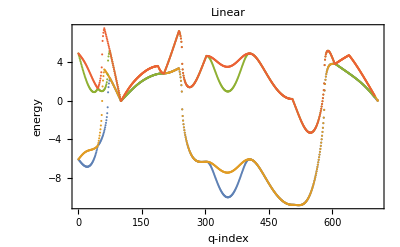

```mathematica
ListPlot[{originalBandA,originalBandB,transformedBandA,transformedBandB},Frame->True,FrameLabel->{"q-index","energy"},PlotLabel->"Linear"]
```

```mathematica
tFunction[Transpose[vo2Data][[7]][[100]],30,0.5]
```

4.12925×10^-7

```mathematica
1/(Exp[(-30*(Transpose[vo2Data][[7]][[100]]-0.5))]+1)
```

4.12925×10^-7

```mathematica
originalBandA[[1;;20]]
```

{{1,-6.05776},{2,-6.11431},{3,-6.17056},{4,-6.22621},{5,-6.28098},{6,-6.3346},{7,-6.38676},{8,-6.43721},{9,-6.48567},{10,-6.53186},{11,-6.57554},{12,-6.61644},{13,-6.65432},{14,-6.68893},{15,-6.72005},{16,-6.74743},{17,-6.77086},{18,-6.79013},{19,-6.80502},{20,-6.81533}}

```mathematica
transformedBandA[[1;;20]]
```

{{1,-6.05776},{2,-6.11431},{3,-6.17056},{4,-6.22621},{5,-6.28098},{6,-6.3346},{7,-6.38676},{8,-6.43721},{9,-6.48567},{10,-6.53186},{11,-6.57554},{12,-6.61644},{13,-6.65432},{14,-6.68893},{15,-6.72005},{16,-6.74743},{17,-6.77086},{18,-6.79013},{19,-6.80502},{20,-6.81533}}

```mathematica
tFunction[arg_,beta_,mu_]:=1/(Exp[-beta*(arg-mu)]+1)


GraphicsGrid[Table[Table[With[{mu=0.25+k/100,beta=5+j},transformedBandA=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[3]][[i]]+tFunction[Transpose[vo2Data][[7]][[i]],beta,mu]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[4]][[i]]+tFunction[Transpose[vo2Data][[7]][[i]],beta,mu]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
ListPlot[{originalBandA,originalBandB,transformedBandA,transformedBandB},Frame->True,ImageSize->300,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]],{k,0,25,2}],{j,0,50,5}]]
```

-Graphics-

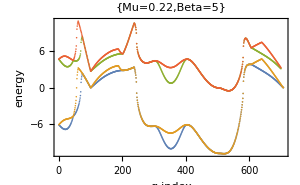
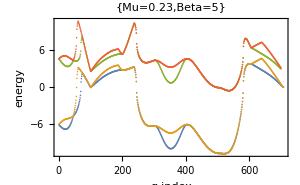
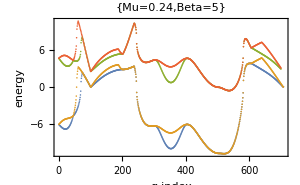
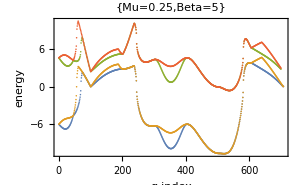
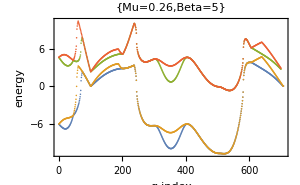
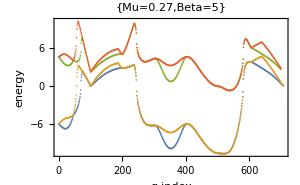
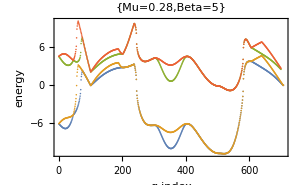
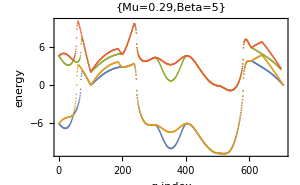

```mathematica
GraphicsGrid[Table[Table[With[{mu=0.01*k,beta=j},transformedBandA=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[3]][[i]]+tFunction[Transpose[vo2Data][[7]][[i]],beta,mu]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[4]][[i]]+tFunction[Transpose[vo2Data][[7]][[i]],beta,mu]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
ListPlot[{originalBandA,originalBandB,transformedBandA,transformedBandB},Frame->True,ImageSize->300,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]],{k,22,38,1}],{j,5,50,5}]]
```

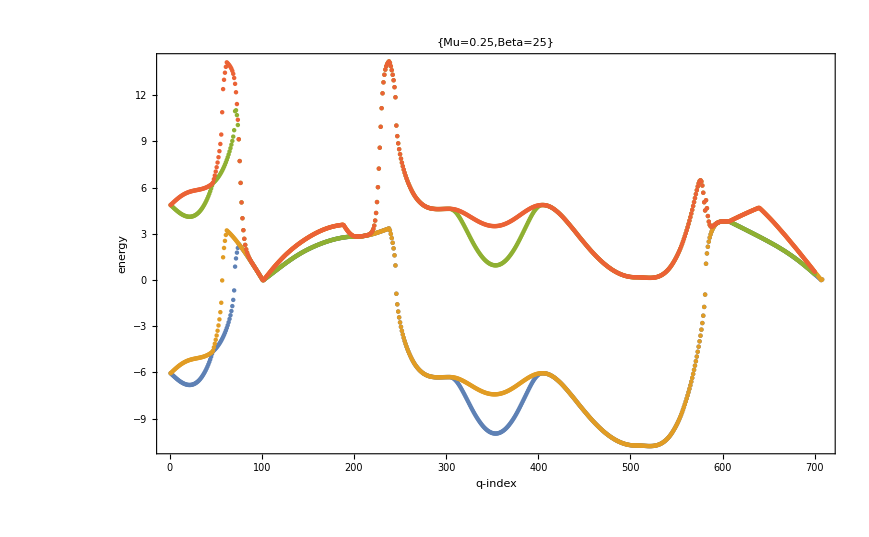

```mathematica
With[{mu=0.25,beta=25},ListPlot[{originalBandA,originalBandB,transformedBandA,transformedBandB},Frame->True,ImageSize->300,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]]
```

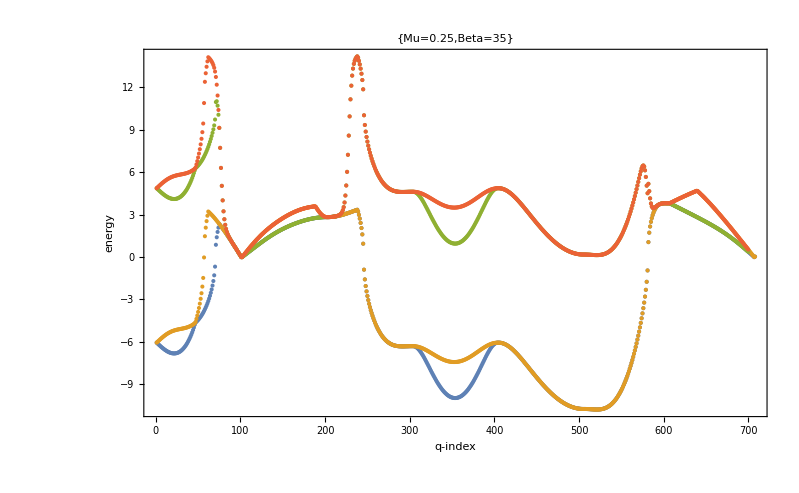

```mathematica
With[{mu=0.25,beta=35},ListPlot[{originalBandA,originalBandB,transformedBandA,transformedBandB},Frame->True,ImageSize->300,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]]
```

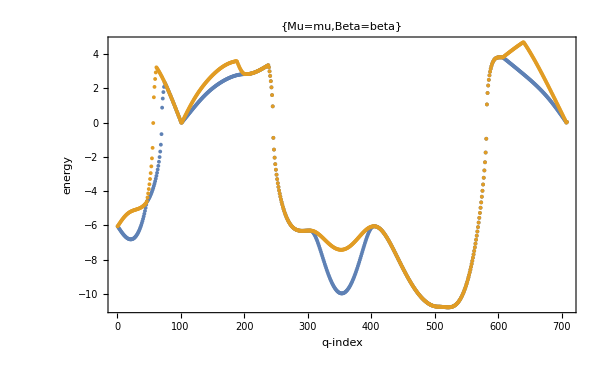

```mathematica
ListPlot[{originalBandA,originalBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]
```

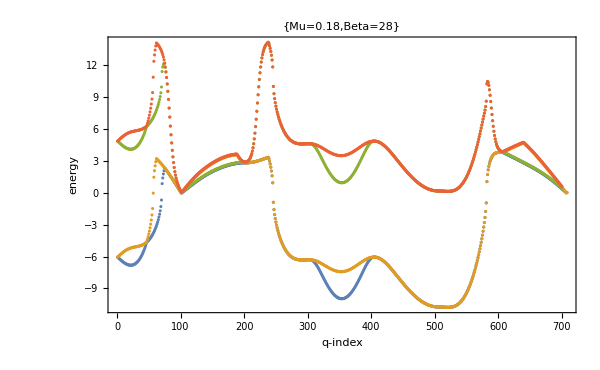

```mathematica
With[{mu=0.01*18,beta=28},transformedBandA=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[3]][[i]]+tFunction[Transpose[vo2Data][[7]][[i]],beta,mu]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[4]][[i]]+tFunction[Transpose[vo2Data][[7]][[i]],beta,mu]*(omega0R^2+Transpose[vo2Data][[6]][[i]]*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
ListPlot[{originalBandA,originalBandB,transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]]
```

```mathematica
mat={{1,2,3},{1,2,3},{4,5,6}}
```

{{1,2,3},{1,2,3},{4,5,6}}

```mathematica
Eigenvalues@mat===Eigenvalues@(5*mat)
```

False

```mathematica
Eigenvectors@mat===Eigenvectors@(5*mat)
```

True

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b/"]
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
list//TableForm
```

0.0625 | 0.0625 | 0.0625 | 1.2847 | 1.81938 | 2.92638 | 4.676 | 0.1875
0.0625 | 0.0625 | 2.07462 | 2.69948 | 4.21313 | 5.17524 | 0.3125 | 0.0625
0.0625 | 2.76936 | 3.86191 | 5.09585 | 5.68261 | 0.4375 | 0.0625 | 0.0625
3.37227 | 3.92313 | 5.74168 | 5.95905 | 0.1875 | 0.1875 | 0.0625 | 1.88443
2.84288 | 4.81338 | 5.66913 | 0.3125 | 0.1875 | 0.0625 | 2.64565 | 3.44945
4.58679 | 6.25959 | 0.4375 | 0.1875 | 0.0625 | 3.36189 | 3.82931 | 5.05908
6.33678 | 0.3125 | 0.3125 | 0.0625 | 2.47653 | 3.54949 | 4.22203 | 6.55926
0.4375 | 0.3125 | 0.0625 | 3.09499 | 3.63158 | 4.24797 | 5.28205 | 0.4375
0.4375 | 0.0625 | 2.85756 | 3.26133 | 4.04884 | 4.33773 | 0.0625 | 0.0625
0.1875 | -3.46639 | 2.57623 | 3.10192 | 4.33458 | 0.1875 | 0.0625 | 0.1875
-4.70577 | -2.08439 | 4.02967 | 5.21924 | 0.3125 | 0.0625 | 0.1875 | -5.65993
-4.32741 | 5.11351 | 5.99083 | 0.4375 | 0.0625 | 0.1875 | -5.97848 | -5.54687
6.05173 | 6.45896 | 0.1875 | 0.1875 | 0.1875 | -5.30176 | 0.793995 | 2.94797
5.82177 | 0.3125 | 0.1875 | 0.1875 | -5.56474 | -2.90663 | 3.97859 | 6.31465
0.4375 | 0.1875 | 0.1875 | -5.29908 | -4.44633 | 5.19439 | 6.17299 | 0.3125
0.3125 | 0.1875 | -4.94692 | 1.03578 | 3.05388 | 6.27475 | 0.4375 | 0.3125
0.1875 | -3.8354 | -2.20354 | 4.23901 | 5.43783 | 0.4375 | 0.4375 | 0.1875
-1.14355 | 2.62383 | 3.34898 | 4.46907 | 0.0625 | 0.0625 | 0.3125 | -6.5392
-5.43531 | 3.94484 | 4.44074 | 0.1875 | 0.0625 | 0.3125 | -8.07257 | -6.7733
4.2202 | 5.19864 | 0.3125 | 0.0625 | 0.3125 | -9.39474 | -8.51118 | 4.81178
5.9699 | 0.4375 | 0.0625 | 0.3125 | -9.98365 | -9.67935 | 5.48304 | 6.09314
0.1875 | 0.1875 | 0.3125 | -9.07185 | -6.31692 | 3.64846 | 6.0553 | 0.3125
0.1875 | 0.3125 | -9.5546 | -7.2281 | 4.01308 | 6.12908 | 0.4375 | 0.1875
0.3125 | -9.36746 | -8.51458 | 4.81559 | 5.65433 | 0.3125 | 0.3125 | 0.3125
-9.04187 | -6.3217 | 3.60926 | 5.80411 | 0.4375 | 0.3125 | 0.3125 | -7.99893
-6.79841 | 4.16884 | 5.04573 | 0.4375 | 0.4375 | 0.3125 | -6.33177 | -5.59102
3.83544 | 4.31885 | 0.0625 | 0.0625 | 0.4375 | -7.20002 | -5.97374 | 4.50222
4.6267 | 0.1875 | 0.0625 | 0.4375 | -8.67581 | -7.40701 | 4.40454 | 4.75463
0.3125 | 0.0625 | 0.4375 | -10.0506 | -9.19507 | 4.25055 | 4.73678 | 0.4375
0.0625 | 0.4375 | -10.6918 | -10.3977 | 4.20767 | 4.45883 | 0.1875 | 0.1875
0.4375 | -9.63967 | -7.16974 | 4.26939 | 4.79284 | 0.3125 | 0.1875 | 0.4375
-10.1691 | -8.05725 | 4.1924 | 4.73363 | 0.4375 | 0.1875 | 0.4375 | -10.048
-9.2624 | 4.24398 | 4.47152 | 0.3125 | 0.3125 | 0.4375 | -9.66251 | -7.27268
4.13429 | 4.48164 | 0.4375 | 0.3125 | 0.4375 | -8.67632 | -7.6184 | 4.09269
4.18331 | 0.4375 | 0.4375 | 0.4375 | -7.09769 | -6.50285 | 3.70538 | 3.70628

```mathematica
list=ReadList["mesh.out",Table[Number,{i,21}]];
fx[band_]:={#[[2]],#[[3]],#[[band+3]]}&/@list;
fy[band_]:={#[[1]],#[[3]],#[[band+3]]}&/@list;
fz[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@list;
```

```mathematica
list[[1]]
```

{0.0625,0.0625,0.0625,1.2847,1.81938,2.92638,4.676,5.50385,5.69044,6.69159,6.71074,11.3827,11.4858,12.2445,12.5314,12.552,12.9132,14.5028,17.3169,17.4325,18.8348}

```mathematica
ListPlot3D[Table[fx[i],{i,1,5}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1]]
```

-Graphics3D-

```mathematica
listd=ReadList["dense_mesh.out",Table[Number,{i,21}]];
fdx[band_]:={#[[2]],#[[3]],#[[band+3]]}&/@listd;
fdy[band_]:={#[[1]],#[[3]],#[[band+3]]}&/@listd;
fdz[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@listd;
```

```mathematica
ListPlot3D[Table[fdx[i],{i,1,5}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1]
```

-Graphics3D-

```mathematica
list//TableForm
```

0.0625 | 0.0625 | 0.0625 | 1.2847 | 1.81938 | 2.92638 | 4.676 | 5.50385 | 5.69044 | 6.69159 | 6.71074 | 11.3827 | 11.4858 | 12.2445 | 12.5314 | 12.552 | 12.9132 | 14.5028 | 17.3169 | 17.4325 | 18.8348
0.1875 | 0.0625 | 0.0625 | 2.07462 | 2.69948 | 4.21313 | 5.17524 | 5.45584 | 6.32999 | 6.75064 | 7.25653 | 10.9398 | 11.2953 | 11.8708 | 12.5446 | 12.5741 | 12.7243 | 14.7745 | 16.9875 | 17.5703 | 19.0024
0.3125 | 0.0625 | 0.0625 | 2.76936 | 3.86191 | 5.09585 | 5.68261 | 5.84434 | 6.89526 | 7.59811 | 8.04089 | 10.2041 | 10.8765 | 11.2667 | 12.08 | 12.6241 | 12.7347 | 15.1972 | 16.5456 | 17.92 | 19.047
0.4375 | 0.0625 | 0.0625 | 3.37227 | 3.92313 | 5.74168 | 5.95905 | 6.63603 | 7.152 | 8.5833 | 9.00651 | 9.37922 | 10.1962 | 10.8978 | 11.4118 | 12.6954 | 12.7407 | 15.6514 | 16.0983 | 18.4055 | 18.836
0.1875 | 0.1875 | 0.0625 | 1.88443 | 2.84288 | 4.81338 | 5.66913 | 5.79478 | 7.015 | 7.30909 | 7.3213 | 10.326 | 11.2659 | 11.4936 | 12.3952 | 12.6517 | 12.6716 | 15.0238 | 17.0883 | 17.5157 | 19.021
0.3125 | 0.1875 | 0.0625 | 2.64565 | 3.44945 | 4.58679 | 6.25959 | 6.66309 | 7.25096 | 7.96902 | 8.1696 | 9.72826 | 10.808 | 11.1665 | 11.9167 | 12.678 | 12.7041 | 15.4523 | 16.8809 | 17.7957 | 18.9581
0.4375 | 0.1875 | 0.0625 | 3.36189 | 3.82931 | 5.05908 | 6.33678 | 6.77752 | 6.89212 | 8.85817 | 9.22596 | 9.67169 | 10.039 | 10.9602 | 11.3029 | 12.6969 | 12.7144 | 15.9502 | 16.4469 | 18.281 | 18.7114
0.3125 | 0.3125 | 0.0625 | 2.47653 | 3.54949 | 4.22203 | 6.55926 | 7.00788 | 7.59938 | 8.43172 | 8.72309 | 9.68173 | 10.6606 | 10.8282 | 11.5368 | 12.6569 | 12.734 | 15.9165 | 17.3031 | 17.6122 | 18.7761
0.4375 | 0.3125 | 0.0625 | 3.09499 | 3.63158 | 4.24797 | 5.28205 | 7.57906 | 7.84296 | 9.20894 | 9.43381 | 9.85417 | 10.0693 | 10.7172 | 11.0298 | 12.68 | 12.7157 | 16.4729 | 17.0051 | 18.0195 | 18.4679
0.4375 | 0.4375 | 0.0625 | 2.85756 | 3.26133 | 4.04884 | 4.33773 | 8.32776 | 8.53456 | 9.51375 | 9.67767 | 9.84909 | 10.063 | 10.3904 | 10.656 | 12.6841 | 12.7003 | 17.0659 | 17.5337 | 17.6711 | 18.1019
0.0625 | 0.0625 | 0.1875 | -3.46639 | 2.57623 | 3.10192 | 4.33458 | 5.06954 | 6.53805 | 6.65578 | 7.90139 | 10.6065 | 10.7356 | 12.1288 | 12.2831 | 12.658 | 12.6873 | 15.9643 | 16.6792 | 16.7226 | 18.6228
0.1875 | 0.0625 | 0.1875 | -4.70577 | -2.08439 | 4.02967 | 5.21924 | 5.481 | 6.57858 | 6.92268 | 8.41911 | 10.1365 | 10.54 | 11.8384 | 11.9835 | 12.6078 | 12.7239 | 16.1151 | 16.6786 | 16.9182 | 18.56
0.3125 | 0.0625 | 0.1875 | -5.65993 | -4.32741 | 5.11351 | 5.99083 | 6.16449 | 6.63919 | 7.38492 | 9.10081 | 9.43199 | 10.2424 | 11.3084 | 11.483 | 12.5467 | 12.6737 | 16.3261 | 16.6717 | 17.2818 | 18.4004
0.4375 | 0.0625 | 0.1875 | -5.97848 | -5.54687 | 6.05173 | 6.45896 | 6.55094 | 6.76968 | 7.85097 | 8.62006 | 9.73941 | 10.2519 | 10.6344 | 10.9356 | 12.5271 | 12.5805 | 16.512 | 16.6279 | 17.7182 | 18.1151
0.1875 | 0.1875 | 0.1875 | -5.30176 | 0.793995 | 2.94797 | 5.82177 | 5.99341 | 6.69916 | 7.31764 | 8.74739 | 9.66707 | 10.5212 | 11.4648 | 11.8007 | 12.5793 | 12.7554 | 16.1994 | 16.6979 | 17.1024 | 18.5066
0.3125 | 0.1875 | 0.1875 | -5.56474 | -2.90663 | 3.97859 | 6.31465 | 6.43637 | 6.91675 | 7.80588 | 9.22774 | 9.252 | 10.2465 | 11.011 | 11.3537 | 12.5836 | 12.7571 | 16.3626 | 16.6974 | 17.4137 | 18.3671
0.4375 | 0.1875 | 0.1875 | -5.29908 | -4.44633 | 5.19439 | 6.17299 | 6.73747 | 6.92024 | 8.39893 | 9.02204 | 9.64024 | 9.9161 | 10.7093 | 10.8761 | 12.6337 | 12.6983 | 16.5343 | 16.6509 | 17.777 | 18.1171
0.3125 | 0.3125 | 0.1875 | -4.94692 | 1.03578 | 3.05388 | 6.27475 | 6.73992 | 7.03738 | 8.35854 | 9.35989 | 9.43955 | 10.1405 | 10.5054 | 11.0451 | 12.676 | 12.8951 | 16.4669 | 16.7133 | 17.6233 | 18.2725
0.4375 | 0.3125 | 0.1875 | -3.8354 | -2.20354 | 4.23901 | 5.43783 | 7.12145 | 7.22682 | 8.91588 | 9.46508 | 9.59582 | 9.6849 | 10.4132 | 10.6663 | 12.8332 | 12.9238 | 16.5979 | 16.6884 | 17.8642 | 18.0976
0.4375 | 0.4375 | 0.1875 | -1.14355 | 2.62383 | 3.34898 | 4.46907 | 7.49025 | 7.54032 | 9.25677 | 9.5055 | 9.53325 | 9.56508 | 10.2648 | 10.4231 | 13.0181 | 13.0563 | 16.6779 | 16.7126 | 17.9543 | 18.0391
0.0625 | 0.0625 | 0.3125 | -6.5392 | -5.43531 | 3.94484 | 4.44074 | 6.05957 | 6.94956 | 7.15214 | 9.12506 | 9.29797 | 10.5507 | 11.0977 | 12.5564 | 12.5759 | 13.2946 | 15.9035 | 16.0142 | 17.2846 | 18.3629
0.1875 | 0.0625 | 0.3125 | -8.07257 | -6.7733 | 4.2202 | 5.19864 | 6.15819 | 6.83198 | 7.35795 | 8.61723 | 9.10434 | 10.7199 | 10.7792 | 12.317 | 12.6477 | 13.2966 | 15.9409 | 16.2522 | 17.2586 | 18.2034
0.3125 | 0.0625 | 0.3125 | -9.39474 | -8.51118 | 4.81178 | 5.9699 | 6.25049 | 6.8568 | 7.45736 | 7.99401 | 8.65097 | 10.082 | 11.0178 | 12.0191 | 12.7613 | 13.2122 | 16.1282 | 16.504 | 17.2277 | 17.9175
0.4375 | 0.0625 | 0.3125 | -9.98365 | -9.67935 | 5.48304 | 6.09314 | 6.62406 | 6.86662 | 7.35032 | 7.66074 | 8.48598 | 9.16205 | 11.3629 | 11.7014 | 12.9134 | 13.0764 | 16.3866 | 16.5685 | 17.3132 | 17.5831
0.1875 | 0.1875 | 0.3125 | -9.07185 | -6.31692 | 3.64846 | 6.0553 | 6.23952 | 6.40783 | 7.81872 | 7.91687 | 9.28978 | 10.5725 | 10.6915 | 12.1137 | 12.4779 | 13.3683 | 15.8201 | 16.5738 | 17.2653 | 18.1539
0.3125 | 0.1875 | 0.3125 | -9.5546 | -7.2281 | 4.01308 | 6.12908 | 6.42578 | 6.70733 | 7.33373 | 8.12362 | 9.14745 | 10.0364 | 10.8248 | 11.6938 | 12.6034 | 13.4061 | 15.8851 | 16.6062 | 17.4346 | 18.0482
0.4375 | 0.1875 | 0.3125 | -9.36746 | -8.51458 | 4.81559 | 5.65433 | 6.53395 | 6.57311 | 7.87357 | 8.26039 | 8.90093 | 9.26824 | 11.0866 | 11.3707 | 12.9326 | 13.2562 | 16.1022 | 16.3846 | 17.6839 | 17.8915
0.3125 | 0.3125 | 0.3125 | -9.04187 | -6.3217 | 3.60926 | 5.80411 | 6.29934 | 6.35278 | 7.98785 | 8.50321 | 9.29377 | 9.86218 | 10.7343 | 11.2196 | 12.6299 | 13.5064 | 15.8293 | 16.4029 | 17.8153 | 18.1736
0.4375 | 0.3125 | 0.3125 | -7.99893 | -6.79841 | 4.16884 | 5.04573 | 6.27648 | 6.30978 | 8.71056 | 8.7211 | 9.12523 | 9.44557 | 10.8177 | 10.9534 | 12.9495 | 13.3378 | 15.9323 | 16.1443 | 18.0945 | 18.2069
0.4375 | 0.4375 | 0.3125 | -6.33177 | -5.59102 | 3.83544 | 4.31885 | 6.20923 | 6.2097 | 8.8428 | 8.95904 | 9.38376 | 9.63512 | 10.6845 | 10.705 | 13.0324 | 13.2195 | 15.9015 | 15.9772 | 18.3532 | 18.3869
0.0625 | 0.0625 | 0.4375 | -7.20002 | -5.97374 | 4.50222 | 4.6267 | 7.28339 | 7.33519 | 7.35501 | 7.37115 | 7.83307 | 9.48848 | 11.797 | 12.6804 | 12.9481 | 13.1019 | 15.2869 | 15.5075 | 18.065 | 18.3245
0.1875 | 0.0625 | 0.4375 | -8.67581 | -7.40701 | 4.40454 | 4.75463 | 6.85512 | 7.08004 | 7.29615 | 7.35242 | 8.02042 | 9.30343 | 11.7338 | 12.2592 | 12.8216 | 13.1145 | 15.291 | 15.8654 | 17.8757 | 18.1617
0.3125 | 0.0625 | 0.4375 | -10.0506 | -9.19507 | 4.25055 | 4.73678 | 6.25836 | 6.76695 | 7.1853 | 7.27834 | 8.04592 | 8.83805 | 11.7008 | 11.9057 | 12.6964 | 12.9826 | 15.5575 | 16.2246 | 17.5339 | 17.8611
0.4375 | 0.0625 | 0.4375 | -10.6918 | -10.3977 | 4.20767 | 4.45883 | 6.04763 | 6.35798 | 7.10095 | 7.20023 | 8.05063 | 8.30397 | 11.7104 | 11.753 | 12.7021 | 12.818 | 15.9927 | 16.3437 | 17.296 | 17.5038
0.1875 | 0.1875 | 0.4375 | -9.63967 | -7.16974 | 4.26939 | 4.79284 | 6.52261 | 6.72466 | 6.94521 | 7.43631 | 8.31256 | 9.21659 | 11.5243 | 11.7444 | 12.9431 | 13.2594 | 14.9826 | 16.4184 | 17.6555 | 18.1844
0.3125 | 0.1875 | 0.4375 | -10.1691 | -8.05725 | 4.1924 | 4.73363 | 6.08705 | 6.41638 | 6.71942 | 7.41374 | 8.42546 | 8.93681 | 11.2873 | 11.446 | 13.0208 | 13.3655 | 15.0704 | 16.5583 | 17.5425 | 18.1266
0.4375 | 0.1875 | 0.4375 | -10.048 | -9.2624 | 4.24398 | 4.47152 | 5.99555 | 6.18935 | 6.73292 | 7.09113 | 8.4689 | 8.61908 | 11.259 | 11.3522 | 13.1671 | 13.3151 | 15.5065 | 16.1039 | 17.7477 | 17.9756
0.3125 | 0.3125 | 0.4375 | -9.66251 | -7.27268 | 4.13429 | 4.48164 | 5.72658 | 6.04173 | 6.73806 | 7.64862 | 8.559 | 8.85888 | 10.8285 | 11.254 | 13.2906 | 13.6735 | 14.9762 | 16.242 | 17.9484 | 18.3375
0.4375 | 0.3125 | 0.4375 | -8.67632 | -7.6184 | 4.09269 | 4.18331 | 5.58951 | 5.66725 | 7.20833 | 7.60894 | 8.56411 | 8.65275 | 10.8373 | 11.0796 | 13.556 | 13.7335 | 15.2381 | 15.7158 | 18.285 | 18.4109
0.4375 | 0.4375 | 0.4375 | -7.09769 | -6.50285 | 3.70538 | 3.70628 | 5.47448 | 5.49831 | 7.75656 | 7.9346 | 8.49396 | 8.52416 | 10.6707 | 10.8337 | 13.7839 | 13.8779 | 15.2417 | 15.4113 | 18.6177 | 18.6559

```mathematica
fx[1]//TableForm
```

0.0625 | 0.0625 | 1.2847
0.0625 | 0.0625 | 2.07462
0.0625 | 0.0625 | 2.76936
0.0625 | 0.0625 | 3.37227
0.1875 | 0.0625 | 1.88443
0.1875 | 0.0625 | 2.64565
0.1875 | 0.0625 | 3.36189
0.3125 | 0.0625 | 2.47653
0.3125 | 0.0625 | 3.09499
0.4375 | 0.0625 | 2.85756
0.0625 | 0.1875 | -3.46639
0.0625 | 0.1875 | -4.70577
0.0625 | 0.1875 | -5.65993
0.0625 | 0.1875 | -5.97848
0.1875 | 0.1875 | -5.30176
0.1875 | 0.1875 | -5.56474
0.1875 | 0.1875 | -5.29908
0.3125 | 0.1875 | -4.94692
0.3125 | 0.1875 | -3.8354
0.4375 | 0.1875 | -1.14355
0.0625 | 0.3125 | -6.5392
0.0625 | 0.3125 | -8.07257
0.0625 | 0.3125 | -9.39474
0.0625 | 0.3125 | -9.98365
0.1875 | 0.3125 | -9.07185
0.1875 | 0.3125 | -9.5546
0.1875 | 0.3125 | -9.36746
0.3125 | 0.3125 | -9.04187
0.3125 | 0.3125 | -7.99893
0.4375 | 0.3125 | -6.33177
0.0625 | 0.4375 | -7.20002
0.0625 | 0.4375 | -8.67581
0.0625 | 0.4375 | -10.0506
0.0625 | 0.4375 | -10.6918
0.1875 | 0.4375 | -9.63967
0.1875 | 0.4375 | -10.1691
0.1875 | 0.4375 | -10.048
0.3125 | 0.4375 | -9.66251
0.3125 | 0.4375 | -8.67632
0.4375 | 0.4375 | -7.09769

```mathematica
list;
```

```mathematica
list//TableForm;
fx[1]//TableForm;
```

```mathematica
fvdxyz[band_]:={#[[1]],#[[2]],#[[3]],#[[band+3]]}&/@listdv[[1;;136]];
```

```mathematica
fvdxy1[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@listdv[[1;;136]];
fvdxy2[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@listdv[[137;;2*136]];
```

```mathematica
ListPlot3D@{fvdxy[1],fvdxy[2],fvdxy[3],fvdxy[4]}
```

-Graphics3D-

```mathematica
ListPlot3D@{fvdxy2[1],fvdxy2[2],fvdxy2[3],fvdxy2[4]}
```

-Graphics3D-

```mathematica
ListInterpolation[{1,2,3}]
```

ListInterpolation::inhr: Requested order is too high; order has been reduced to {2}.

InterpolatingFunction[{{1, 3}}, <>]

```mathematica
fInt[0,0,0]
```

Interpolation[{{0.015625,0.015625,0.330584},{0.015625,0.015625,0.591688},{0.015625,0.015625,0.919632},2170,{0.453125,0.484375,-6.76182},{0.453125,0.484375,-6.5319},{0.484375,0.484375,-6.36327}}][0,0,0]
 |  |  |  |

```mathematica
fIn=Interpolation[fvdxyz[1]]
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{0.015625, 0.484375}, {0.015625, 0.484375}, {0.015625, 0.484375}}, <>]

```mathematica
fInt[]
```

```mathematica
listdv=ReadList["vdense_mesh.out",Table[Number,{i,21}]];
fvdx[band_]:={#[[2]],#[[3]],#[[band+3]]}&/@listdv;
fvdy[band_]:={#[[1]],#[[3]],#[[band+3]]}&/@listdv;
fvdz[band_]:={#[[1]],#[[2]],#[[band+3]]}&/@listdv;
```

```mathematica
ListPlot3D[Table[fvdx[i],{i,1}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1,AxesLabel->{"y","z","frequency"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdy[i],{i,1}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1,AxesLabel->{"x","z","frequency"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdy[i],{i,2,2}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1,AxesLabel->{"x","z","frequency"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdx[i],{i,2,2}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1,AxesLabel->{"y","z","frequency"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdx[i],{i,3,3}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1,AxesLabel->{"y","z","frequency"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fx[i],{i,1,4,1}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1,AxesLabel->{"x","z","frequency"}]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdy[i],{i,1,3,1}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdx[i],{i,1,3,1}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1]
```

-Graphics3D-

```mathematica
ListPlot3D[Table[fvdx[i],{i,1,4,1}],AspectRatio->1,ImageSize->700,PlotStyle->Opacity[0.1],InterpolationOrder->1]
```

-Graphics3D-

```mathematica
ListPlot3D@fvdx[1]
ListPlot3D@fvdy[1]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPlot3D@fvdx[2]
ListPlot3D@fvdy[2]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListPointPlot3D@fy[1]
```

-Graphics3D-